```mathematica
ColorMainMatrix17[graph_,graphFormat_:FormatGraph,vertices_:Null]:=Block[{sols,result,bg, sorted},
PrintTemporary["Solving g.." ];
sorted=Graph[Sort[VertexList[graph]],Sort[EdgeList[graph],EdgeComp]];
sols=Solve[ToEquations[sorted],SymbolRange[sorted]];
PrintTemporary["Solved g" ];
result=TableForm[
Table[
bg=None;
If[i≤j,
Framed[
With[
{
mat=ColorSubMatrix[sols,i,j]
},

If[mat[[1]]==0,bg=LightRed];
If[MemberQ[vertices,i]&&MemberQ[vertices,j],bg=LightRed];
If[i==j,bg=LightYellow];
If[EdgeQ[sorted,i<->j],bg=LightBlue];
TableForm[mat]
],
Background->bg
],
""
],
{i,vertices//Sort},
{j,vertices//Sort}],
TableHeadings->{vertices//Sort, vertices//Sort},
TableSpacing->{0, 0}
];
{graphFormat[sorted],result}
]
```

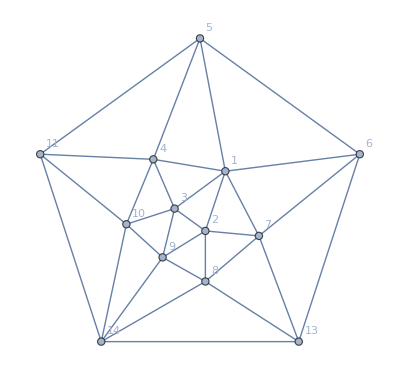

```mathematica
Graph[VertexDelete[Graph[plantri[[2]]],12],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
Table[
With[
{g=EdgeAdd[VertexDelete[Graph[plantri[[2]]],12],edges]},
Labeled[ColorMainMatrix17[g,Graph[#,VertexLabels->"Name",GraphLayout->If[PlanarGraphQ[#],"TutteEmbedding","SpringElectricalEmbedding"],PlotLabel->{ChromaticPolynomial[#,4]/24},ImageSize->120,EdgeStyle->Map[#->Red&,edges]]&,{5,6,13,14,11}],
edges]
]
,{edges,Subsets[EdgeList[GraphComplement[Graph[{5<->6,6<->13,13<->14,14<->11,11<->5}]]]]}]
```

{{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 40
0 | 0
40 | 0
40 | 8
32 | 13
27
6 |  | 40
0 | 8
32 | 0
40 | 13
27
11 |  |  | 40
0 | 18
22 | 0
40
13 |  |  |  | 40
0 | 0
40
14 |  |  |  |  | 40
0}{},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 32
0 | 0
32 | 0
32 | 0
32 | 13
19
6 |  | 32
0 | 6
26 | 0
32 | 10
22
11 |  |  | 32
0 | 18
14 | 0
32
13 |  |  |  | 32
0 | 0
32
14 |  |  |  |  | 32
0}{5<->13},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 27
0 | 0
27 | 0
27 | 8
19 | 0
27
6 |  | 27
0 | 5
22 | 0
27 | 13
14
11 |  |  | 27
0 | 12
15 | 0
27
13 |  |  |  | 27
0 | 0
27
14 |  |  |  |  | 27
0}{5<->14},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 27
0 | 0
27 | 0
27 | 5
22 | 13
14
6 |  | 27
0 | 8
19 | 0
27 | 0
27
11 |  |  | 27
0 | 12
15 | 0
27
13 |  |  |  | 27
0 | 0
27
14 |  |  |  |  | 27
0}{6<->14},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 32
0 | 0
32 | 0
32 | 6
26 | 10
22
6 |  | 32
0 | 0
32 | 0
32 | 13
19
11 |  |  | 32
0 | 18
14 | 0
32
13 |  |  |  | 32
0 | 0
32
14 |  |  |  |  | 32
0}{6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 22
0 | 0
22 | 0
22 | 8
14 | 7
15
6 |  | 22
0 | 8
14 | 0
22 | 7
15
11 |  |  | 22
0 | 0
22 | 0
22
13 |  |  |  | 22
0 | 0
22
14 |  |  |  |  | 22
0}{13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 19
0 | 0
19 | 0
19 | 0
19 | 0
19
6 |  | 19
0 | 3
16 | 0
19 | 10
9
11 |  |  | 19
0 | 12
7 | 0
19
13 |  |  |  | 19
0 | 0
19
14 |  |  |  |  | 19
0}{5<->13,5<->14},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 22
0 | 0
22 | 0
22 | 0
22 | 13
9
6 |  | 22
0 | 6
16 | 0
22 | 0
22
11 |  |  | 22
0 | 12
10 | 0
22
13 |  |  |  | 22
0 | 0
22
14 |  |  |  |  | 22
0}{5<->13,6<->14},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 26
0 | 0
26 | 0
26 | 0
26 | 10
16
6 |  | 26
0 | 0
26 | 0
26 | 10
16
11 |  |  | 26
0 | 18
8 | 0
26
13 |  |  |  | 26
0 | 0
26
14 |  |  |  |  | 26
0}{5<->13,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 14
0 | 0
14 | 0
14 | 0
14 | 7
7
6 |  | 14
0 | 6
8 | 0
14 | 4
10
11 |  |  | 14
0 | 0
14 | 0
14
13 |  |  |  | 14
0 | 0
14
14 |  |  |  |  | 14
0}{5<->13,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 14
0 | 0
14 | 0
14 | 5
9 | 0
14
6 |  | 14
0 | 5
9 | 0
14 | 0
14
11 |  |  | 14
0 | 6
8 | 0
14
13 |  |  |  | 14
0 | 0
14
14 |  |  |  |  | 14
0}{5<->14,6<->14},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 22
0 | 0
22 | 0
22 | 6
16 | 0
22
6 |  | 22
0 | 0
22 | 0
22 | 13
9
11 |  |  | 22
0 | 12
10 | 0
22
13 |  |  |  | 22
0 | 0
22
14 |  |  |  |  | 22
0}{5<->14,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 15
0 | 0
15 | 0
15 | 8
7 | 0
15
6 |  | 15
0 | 5
10 | 0
15 | 7
8
11 |  |  | 15
0 | 0
15 | 0
15
13 |  |  |  | 15
0 | 0
15
14 |  |  |  |  | 15
0}{5<->14,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 19
0 | 0
19 | 0
19 | 3
16 | 10
9
6 |  | 19
0 | 0
19 | 0
19 | 0
19
11 |  |  | 19
0 | 12
7 | 0
19
13 |  |  |  | 19
0 | 0
19
14 |  |  |  |  | 19
0}{6<->14,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 15
0 | 0
15 | 0
15 | 5
10 | 7
8
6 |  | 15
0 | 8
7 | 0
15 | 0
15
11 |  |  | 15
0 | 0
15 | 0
15
13 |  |  |  | 15
0 | 0
15
14 |  |  |  |  | 15
0}{6<->14,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 14
0 | 0
14 | 0
14 | 6
8 | 4
10
6 |  | 14
0 | 0
14 | 0
14 | 7
7
11 |  |  | 14
0 | 0
14 | 0
14
13 |  |  |  | 14
0 | 0
14
14 |  |  |  |  | 14
0}{6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 9
0 | 0
9 | 0
9 | 0
9 | 0
9
6 |  | 9
0 | 3
6 | 0
9 | 0
9
11 |  |  | 9
0 | 6
3 | 0
9
13 |  |  |  | 9
0 | 0
9
14 |  |  |  |  | 9
0}{5<->13,5<->14,6<->14},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 16
0 | 0
16 | 0
16 | 0
16 | 0
16
6 |  | 16
0 | 0
16 | 0
16 | 10
6
11 |  |  | 16
0 | 12
4 | 0
16
13 |  |  |  | 16
0 | 0
16
14 |  |  |  |  | 16
0}{5<->13,5<->14,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 7
0 | 0
7 | 0
7 | 0
7 | 0
7
6 |  | 7
0 | 3
4 | 0
7 | 4
3
11 |  |  | 7
0 | 0
7 | 0
7
13 |  |  |  | 7
0 | 0
7
14 |  |  |  |  | 7
0}{5<->13,5<->14,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 16
0 | 0
16 | 0
16 | 0
16 | 10
6
6 |  | 16
0 | 0
16 | 0
16 | 0
16
11 |  |  | 16
0 | 12
4 | 0
16
13 |  |  |  | 16
0 | 0
16
14 |  |  |  |  | 16
0}{5<->13,6<->14,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 10
0 | 0
10 | 0
10 | 0
10 | 7
3
6 |  | 10
0 | 6
4 | 0
10 | 0
10
11 |  |  | 10
0 | 0
10 | 0
10
13 |  |  |  | 10
0 | 0
10
14 |  |  |  |  | 10
0}{5<->13,6<->14,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 8
0 | 0
8 | 0
8 | 0
8 | 4
4
6 |  | 8
0 | 0
8 | 0
8 | 4
4
11 |  |  | 8
0 | 0
8 | 0
8
13 |  |  |  | 8
0 | 0
8
14 |  |  |  |  | 8
0}{5<->13,6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 9
0 | 0
9 | 0
9 | 3
6 | 0
9
6 |  | 9
0 | 0
9 | 0
9 | 0
9
11 |  |  | 9
0 | 6
3 | 0
9
13 |  |  |  | 9
0 | 0
9
14 |  |  |  |  | 9
0}{5<->14,6<->14,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 8
0 | 0
8 | 0
8 | 5
3 | 0
8
6 |  | 8
0 | 5
3 | 0
8 | 0
8
11 |  |  | 8
0 | 0
8 | 0
8
13 |  |  |  | 8
0 | 0
8
14 |  |  |  |  | 8
0}{5<->14,6<->14,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 10
0 | 0
10 | 0
10 | 6
4 | 0
10
6 |  | 10
0 | 0
10 | 0
10 | 7
3
11 |  |  | 10
0 | 0
10 | 0
10
13 |  |  |  | 10
0 | 0
10
14 |  |  |  |  | 10
0}{5<->14,6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 7
0 | 0
7 | 0
7 | 3
4 | 4
3
6 |  | 7
0 | 0
7 | 0
7 | 0
7
11 |  |  | 7
0 | 0
7 | 0
7
13 |  |  |  | 7
0 | 0
7
14 |  |  |  |  | 7
0}{6<->14,6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 6
0 | 0
6 | 0
6 | 0
6 | 0
6
6 |  | 6
0 | 0
6 | 0
6 | 0
6
11 |  |  | 6
0 | 6
0 | 0
6
13 |  |  |  | 6
0 | 0
6
14 |  |  |  |  | 6
0}{5<->13,5<->14,6<->14,6<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 3
0 | 0
3 | 0
3 | 0
3 | 0
3
6 |  | 3
0 | 3
0 | 0
3 | 0
3
11 |  |  | 3
0 | 0
3 | 0
3
13 |  |  |  | 3
0 | 0
3
14 |  |  |  |  | 3
0}{5<->13,5<->14,6<->14,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 4
0 | 0
4 | 0
4 | 0
4 | 0
4
6 |  | 4
0 | 0
4 | 0
4 | 4
0
11 |  |  | 4
0 | 0
4 | 0
4
13 |  |  |  | 4
0 | 0
4
14 |  |  |  |  | 4
0}{5<->13,5<->14,6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 4
0 | 0
4 | 0
4 | 0
4 | 4
0
6 |  | 4
0 | 0
4 | 0
4 | 0
4
11 |  |  | 4
0 | 0
4 | 0
4
13 |  |  |  | 4
0 | 0
4
14 |  |  |  |  | 4
0}{5<->13,6<->14,6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 3
0 | 0
3 | 0
3 | 3
0 | 0
3
6 |  | 3
0 | 0
3 | 0
3 | 0
3
11 |  |  | 3
0 | 0
3 | 0
3
13 |  |  |  | 3
0 | 0
3
14 |  |  |  |  | 3
0}{5<->14,6<->14,6<->11,13<->11},{-Graphics-, | 5 | 6 | 11 | 13 | 14
5 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0
6 |  | 0
0 | 0
0 | 0
0 | 0
0
11 |  |  | 0
0 | 0
0 | 0
0
13 |  |  |  | 0
0 | 0
0
14 |  |  |  |  | 0
0}{5<->13,5<->14,6<->14,6<->11,13<->11}}

```mathematica
Table[
With[
{g=EdgeAdd[VertexDelete[Graph[plantri[[1]]],1],edges]},
Labeled[ColorMainMatrix17[g,Graph[#,VertexLabels->"Name",GraphLayout->If[PlanarGraphQ[#],"TutteEmbedding","SpringElectricalEmbedding"],PlotLabel->{ChromaticPolynomial[#,4]/24},ImageSize->120,EdgeStyle->Map[#->Red&,edges]]&,{2,3,4,5,6}],
edges]
]
,{edges,Subsets[EdgeList[GraphComplement[Graph[{2<->3,3<->4,4<->5,5<->6,6<->2}]]]]}]
```

{{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 20
0 | 0
20 | 6
14 | 6
14 | 0
20
3 |  | 20
0 | 0
20 | 6
14 | 6
14
4 |  |  | 20
0 | 0
20 | 6
14
5 |  |  |  | 20
0 | 0
20
6 |  |  |  |  | 20
0}{},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 14
0 | 0
14 | 0
14 | 6
8 | 0
14
3 |  | 14
0 | 0
14 | 4
10 | 4
10
4 |  |  | 14
0 | 0
14 | 6
8
5 |  |  |  | 14
0 | 0
14
6 |  |  |  |  | 14
0}{2<->4},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 14
0 | 0
14 | 6
8 | 0
14 | 0
14
3 |  | 14
0 | 0
14 | 6
8 | 4
10
4 |  |  | 14
0 | 0
14 | 4
10
5 |  |  |  | 14
0 | 0
14
6 |  |  |  |  | 14
0}{2<->5},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 14
0 | 0
14 | 4
10 | 6
8 | 0
14
3 |  | 14
0 | 0
14 | 0
14 | 6
8
4 |  |  | 14
0 | 0
14 | 4
10
5 |  |  |  | 14
0 | 0
14
6 |  |  |  |  | 14
0}{3<->5},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 14
0 | 0
14 | 4
10 | 4
10 | 0
14
3 |  | 14
0 | 0
14 | 6
8 | 0
14
4 |  |  | 14
0 | 0
14 | 6
8
5 |  |  |  | 14
0 | 0
14
6 |  |  |  |  | 14
0}{3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 14
0 | 0
14 | 6
8 | 4
10 | 0
14
3 |  | 14
0 | 0
14 | 4
10 | 6
8
4 |  |  | 14
0 | 0
14 | 0
14
5 |  |  |  | 14
0 | 0
14
6 |  |  |  |  | 14
0}{4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 8
0 | 0
8 | 0
8 | 0
8 | 0
8
3 |  | 8
0 | 0
8 | 4
4 | 2
6
4 |  |  | 8
0 | 0
8 | 4
4
5 |  |  |  | 8
0 | 0
8
6 |  |  |  |  | 8
0}{2<->4,2<->5},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 10
0 | 0
10 | 0
10 | 6
4 | 0
10
3 |  | 10
0 | 0
10 | 0
10 | 4
6
4 |  |  | 10
0 | 0
10 | 4
6
5 |  |  |  | 10
0 | 0
10
6 |  |  |  |  | 10
0}{2<->4,3<->5},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 10
0 | 0
10 | 0
10 | 4
6 | 0
10
3 |  | 10
0 | 0
10 | 4
6 | 0
10
4 |  |  | 10
0 | 0
10 | 6
4
5 |  |  |  | 10
0 | 0
10
6 |  |  |  |  | 10
0}{2<->4,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 8
0 | 0
8 | 0
8 | 4
4 | 0
8
3 |  | 8
0 | 0
8 | 2
6 | 4
4
4 |  |  | 8
0 | 0
8 | 0
8
5 |  |  |  | 8
0 | 0
8
6 |  |  |  |  | 8
0}{2<->4,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 8
0 | 0
8 | 4
4 | 0
8 | 0
8
3 |  | 8
0 | 0
8 | 0
8 | 4
4
4 |  |  | 8
0 | 0
8 | 2
6
5 |  |  |  | 8
0 | 0
8
6 |  |  |  |  | 8
0}{2<->5,3<->5},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 10
0 | 0
10 | 4
6 | 0
10 | 0
10
3 |  | 10
0 | 0
10 | 6
4 | 0
10
4 |  |  | 10
0 | 0
10 | 4
6
5 |  |  |  | 10
0 | 0
10
6 |  |  |  |  | 10
0}{2<->5,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 10
0 | 0
10 | 6
4 | 0
10 | 0
10
3 |  | 10
0 | 0
10 | 4
6 | 4
6
4 |  |  | 10
0 | 0
10 | 0
10
5 |  |  |  | 10
0 | 0
10
6 |  |  |  |  | 10
0}{2<->5,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 8
0 | 0
8 | 2
6 | 4
4 | 0
8
3 |  | 8
0 | 0
8 | 0
8 | 0
8
4 |  |  | 8
0 | 0
8 | 4
4
5 |  |  |  | 8
0 | 0
8
6 |  |  |  |  | 8
0}{3<->5,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10
3 |  | 10
0 | 0
10 | 0
10 | 6
4
4 |  |  | 10
0 | 0
10 | 0
10
5 |  |  |  | 10
0 | 0
10
6 |  |  |  |  | 10
0}{3<->5,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 8
0 | 0
8 | 4
4 | 2
6 | 0
8
3 |  | 8
0 | 0
8 | 4
4 | 0
8
4 |  |  | 8
0 | 0
8 | 0
8
5 |  |  |  | 8
0 | 0
8
6 |  |  |  |  | 8
0}{3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 4
0 | 0
4 | 0
4 | 0
4 | 0
4
3 |  | 4
0 | 0
4 | 0
4 | 2
2
4 |  |  | 4
0 | 0
4 | 2
2
5 |  |  |  | 4
0 | 0
4
6 |  |  |  |  | 4
0}{2<->4,2<->5,3<->5},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 6
0 | 0
6 | 0
6 | 0
6 | 0
6
3 |  | 6
0 | 0
6 | 4
2 | 0
6
4 |  |  | 6
0 | 0
6 | 4
2
5 |  |  |  | 6
0 | 0
6
6 |  |  |  |  | 6
0}{2<->4,2<->5,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 4
0 | 0
4 | 0
4 | 0
4 | 0
4
3 |  | 4
0 | 0
4 | 2
2 | 2
2
4 |  |  | 4
0 | 0
4 | 0
4
5 |  |  |  | 4
0 | 0
4
6 |  |  |  |  | 4
0}{2<->4,2<->5,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 6
0 | 0
6 | 0
6 | 4
2 | 0
6
3 |  | 6
0 | 0
6 | 0
6 | 0
6
4 |  |  | 6
0 | 0
6 | 4
2
5 |  |  |  | 6
0 | 0
6
6 |  |  |  |  | 6
0}{2<->4,3<->5,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 6
0 | 0
6 | 0
6 | 4
2 | 0
6
3 |  | 6
0 | 0
6 | 0
6 | 4
2
4 |  |  | 6
0 | 0
6 | 0
6
5 |  |  |  | 6
0 | 0
6
6 |  |  |  |  | 6
0}{2<->4,3<->5,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 4
0 | 0
4 | 0
4 | 2
2 | 0
4
3 |  | 4
0 | 0
4 | 2
2 | 0
4
4 |  |  | 4
0 | 0
4 | 0
4
5 |  |  |  | 4
0 | 0
4
6 |  |  |  |  | 4
0}{2<->4,3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 4
0 | 0
4 | 2
2 | 0
4 | 0
4
3 |  | 4
0 | 0
4 | 0
4 | 0
4
4 |  |  | 4
0 | 0
4 | 2
2
5 |  |  |  | 4
0 | 0
4
6 |  |  |  |  | 4
0}{2<->5,3<->5,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 6
0 | 0
6 | 4
2 | 0
6 | 0
6
3 |  | 6
0 | 0
6 | 0
6 | 4
2
4 |  |  | 6
0 | 0
6 | 0
6
5 |  |  |  | 6
0 | 0
6
6 |  |  |  |  | 6
0}{2<->5,3<->5,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 6
0 | 0
6 | 4
2 | 0
6 | 0
6
3 |  | 6
0 | 0
6 | 4
2 | 0
6
4 |  |  | 6
0 | 0
6 | 0
6
5 |  |  |  | 6
0 | 0
6
6 |  |  |  |  | 6
0}{2<->5,3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 4
0 | 0
4 | 2
2 | 2
2 | 0
4
3 |  | 4
0 | 0
4 | 0
4 | 0
4
4 |  |  | 4
0 | 0
4 | 0
4
5 |  |  |  | 4
0 | 0
4
6 |  |  |  |  | 4
0}{3<->5,3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 2
0 | 0
2 | 0
2 | 0
2 | 0
2
3 |  | 2
0 | 0
2 | 0
2 | 0
2
4 |  |  | 2
0 | 0
2 | 2
0
5 |  |  |  | 2
0 | 0
2
6 |  |  |  |  | 2
0}{2<->4,2<->5,3<->5,3<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 2
0 | 0
2 | 0
2 | 0
2 | 0
2
3 |  | 2
0 | 0
2 | 0
2 | 2
0
4 |  |  | 2
0 | 0
2 | 0
2
5 |  |  |  | 2
0 | 0
2
6 |  |  |  |  | 2
0}{2<->4,2<->5,3<->5,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 2
0 | 0
2 | 0
2 | 0
2 | 0
2
3 |  | 2
0 | 0
2 | 2
0 | 0
2
4 |  |  | 2
0 | 0
2 | 0
2
5 |  |  |  | 2
0 | 0
2
6 |  |  |  |  | 2
0}{2<->4,2<->5,3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 2
0 | 0
2 | 0
2 | 2
0 | 0
2
3 |  | 2
0 | 0
2 | 0
2 | 0
2
4 |  |  | 2
0 | 0
2 | 0
2
5 |  |  |  | 2
0 | 0
2
6 |  |  |  |  | 2
0}{2<->4,3<->5,3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 2
0 | 0
2 | 2
0 | 0
2 | 0
2
3 |  | 2
0 | 0
2 | 0
2 | 0
2
4 |  |  | 2
0 | 0
2 | 0
2
5 |  |  |  | 2
0 | 0
2
6 |  |  |  |  | 2
0}{2<->5,3<->5,3<->6,4<->6},{-Graphics-, | 2 | 3 | 4 | 5 | 6
2 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0
3 |  | 0
0 | 0
0 | 0
0 | 0
0
4 |  |  | 0
0 | 0
0 | 0
0
5 |  |  |  | 0
0 | 0
0
6 |  |  |  |  | 0
0}{2<->4,2<->5,3<->5,3<->6,4<->6}}